```mathematica
(*Function to Create a Calendar for a Given Month and Year*)CreateCalendar[year_,month_]:=Module[{firstDay,daysInMonth,weekdays,dayLabels,grid,calendarData},(*Determine the first day of the month and number of days*)firstDay=DayName[{year,month,1}];
daysInMonth=DayRange[{year,month,1},{year,month,"EndOfMonth"}];
(*Weekday Labels*)weekdays={"Sun","Mon","Tue","Wed","Thu","Fri","Sat"};
dayLabels=Style[#,Bold,14,RGBColor[0.2,0.4,0.6]]&/@weekdays;
(*Arrange Days in a Grid*)grid=ConstantArray["",{6,7}];
Do[grid[[Quotient[i-1+FirstPosition[weekdays,firstDay][[1]],7]+1,Mod[i-1+FirstPosition[weekdays,firstDay][[1]],7]+1]]=Style[ToString[daysInMonth[[i,3]]],14],{i,Length[daysInMonth]}];
(*Add Day Labels to the Grid*)calendarData=Join[{dayLabels},grid];
(*Display Calendar as a Grid*)Grid[calendarData,Spacings->{2,2},Frame->All,Background->{None,{{GrayLevel[0.95],None}}},Dividers->{False,True}]];

(*Generate the Calendar for January 2025*)
CreateCalendar[2025,1]
```

Set::shape: Lists {System`InternalDateUtilitiesDump`cal2$318228,System`InternalDateUtilitiesDump`y2$318228,System`InternalDateUtilitiesDump`m2$318228,System`InternalDateUtilitiesDump`d2$318228,System`InternalDateUtilitiesDump`h2$318228,System`InternalDateUtilitiesDump`mm2$318228,System`InternalDateUtilitiesDump`s2$318228} and DateAndTime`PadCalendarDate[DateAndTime`PadCalendarDate[System`InternalDateUtilitiesDump`dropZeros[Gregorian,DateList[{2025,1,EndOfMonth}],3]]] are not the same shape.

Part::take: Cannot take positions 2 through 4 in DateAndTime`PadCalendarDate[System`InternalDateUtilitiesDump`dropZeros[Gregorian,DateList[{2025,1,EndOfMonth}],3]].

Range::range: Range specification in Range[739257,$Failed,7] does not have appropriate bounds.

Range::range: Range specification in Range[739258,$Failed,7] does not have appropriate bounds.

Range::range: Range specification in Range[739252,$Failed,7] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

DateObject::date: Expression {System`DateCalendarsDump`dateListPrecisionHandler[System`DateCalendarsDump`dateYearZeroHandler[Internal`DateListToDateList[DateAndTime`JulianDateToDateList[3442849/2+Range[739252,$Failed,7]]],True,1],Range[739252,$Failed,7]],System`DateCalendarsDump`dateListPrecisionHandler[«1»,Range[739253,$Failed,7]],System`DateCalendarsDump`dateListPrecisionHandler[System`DateCalendarsDump`dateYearZeroHandler[Internal`DateListToDateList[DateAndTime`JulianDateToDateList[3442849/2+Range[739254,$Failed,7]]],True,1],Range[739254,$Failed,7]]} cannot be interpreted as a date specification.

Set::pkspec1: The expression 1+Quotient[NotFound,7] cannot be used as a part specification.

Part::partd: Part specification «1» is longer than depth of object.

Set::pkspec1: The expression 1+Quotient[1+NotFound,7] cannot be used as a part specification.

Part::partw: Part 3 of CalendarType→Gregorian does not exist.

Set::pkspec1: The expression 1+Quotient[2+NotFound,7] cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

```mathematica
{{"Sun", "Mon", "Tue", "Wed", "Thu", "Fri", "Sat"}, {"", "", "", "", "", "", ""}, {□, "", "", "", "", "", ""}, {"", "", "", "", "", "", ""}, {"", "", "", "", "", "", ""}, {"", "", "", "", "", "", ""}, {"", "", "", "", "", "", ""}}
```

```mathematica
TableView[List/@DateString/@DateRange[Tomorrow, DatePlus[Tomorrow, 7]]]
```

Wed 15 Jan 2025Thu 16 Jan 2025Fri 17 Jan 2025Sat 18 Jan 2025Sun 19 Jan 2025Mon 20 Jan 2025Tue 21 Jan 2025Wed 22 Jan 2025

```mathematica
Graphics[{White, Text["Hello"]}]
```

-Graphics-

```mathematica
TimelinePlot[]
```

```mathematica
(*Define a Weekly Schedule*)schedule={<|"Day"->"Wednesday","Time"->"5:00 PM - 12:00 AM","Task"->"Available"|>,
<|"Day"->"Thursday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,
<|"Day"->"Friday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,
<|"Day"->"Saturday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,
<|"Day"->"Sunday","Time"->"7:00 PM - 12:00 AM","Task"->"Available"|>}
```

{<|Day→Wednesday,Time→5:00 PM - 12:00 AM,Task→Available|>,<|Day→Thursday,Time→9:00 AM - 5:00 PM,Task→Available|>,<|Day→Friday,Time→9:00 AM - 5:00 PM,Task→Available|>,<|Day→Saturday,Time→9:00 AM - 5:00 PM,Task→Available|>,<|Day→Sunday,Time→7:00 PM - 12:00 AM,Task→Available|>}

```mathematica
Dataset[schedule]
```

```mathematica
(*Convert Schedule to Timeline Data*)timelineData=KeyValueMap[Function[{key,values},Placed[values["Task"],Above]->Interval[DateObject[{2025,1,13+Position[{"Monday","Tuesday","Wednesday","Thursday","Friday"},values["Day"]][[1,1]]},"Day"],QuantityMagnitude[DateObject[{2025,1}<>Quantity]]
```

```mathematica
(*Convert Schedule to Timeline Data*)timelineData=KeyValueMap[Function[{key,values},Placed[values["Task"],Above]->Interval[DateObject[{2025,1,13+Position[{"Monday","Tuesday","Wednesday","Thursday","Friday"},values["Day"]][[1,1]]},"Day"],QuantityMagnitude[DateObject[{2025,1}<>Quantity]]
```

```mathematica
schedule={<|"Day"->"Wednesday","Time"->"5:00 PM - 12:00 AM","Task"->"Available"|>,<|"Day"->"Thursday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,<|"Day"->"Friday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,<|"Day"->"Saturday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,<|"Day"->"Sunday","Time"->"7:00 PM - 12:00 AM","Task"->"Available"|>};

(*Function to convert a schedule entry to a DateInterval*)
timeStringToDateInterval[day_,time_]:=Module[{start,end},{start,end}=StringSplit[time," - "]//DateObject[{day,#},{"DayName","Hour12:Minute AMPM"}]&;
DateInterval[{start,end}]];

(*Convert all schedule entries into DateIntervals*)
dateIntervals=schedule/. <|"Day"->day_,"Time"->time_,"Task"->task_|>:>{task,timeStringToDateInterval[day,time]};
```

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

Set::shape: Lists {start$329051,end$329051} and DateObject[{Wednesday,{5:00 PM,12:00 AM}},{DayName,Hour12:Minute AMPM}] are not the same shape.

DateInterval::arg: Argument {start$329051,end$329051} cannot be interpreted as a date or time input.

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

Set::shape: Lists {start$329076,end$329076} and DateObject[{Thursday,{9:00 AM,5:00 PM}},{DayName,Hour12:Minute AMPM}] are not the same shape.

DateInterval::arg: Argument {start$329076,end$329076} cannot be interpreted as a date or time input.

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

General::stop: Further output of DateObject::notgran will be suppressed during this calculation.

Set::shape: Lists {start$329101,end$329101} and DateObject[{Friday,{9:00 AM,5:00 PM}},{DayName,Hour12:Minute AMPM}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

DateInterval::arg: Argument {start$329101,end$329101} cannot be interpreted as a date or time input.

General::stop: Further output of DateInterval::arg will be suppressed during this calculation.

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

Set::shape: Lists {start$327663,end$327663} and DateObject[{Wednesday,{5:00 PM,12:00 AM}},{DayName,Hour12:Minute AMPM}] are not the same shape.

DateInterval::arg: Argument {start$327663,end$327663} cannot be interpreted as a date or time input.

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

Set::shape: Lists {start$328077,end$328077} and DateObject[{Thursday,{9:00 AM,5:00 PM}},{DayName,Hour12:Minute AMPM}] are not the same shape.

DateInterval::arg: Argument {start$328077,end$328077} cannot be interpreted as a date or time input.

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

General::stop: Further output of DateObject::notgran will be suppressed during this calculation.

Set::shape: Lists {start$328102,end$328102} and DateObject[{Friday,{9:00 AM,5:00 PM}},{DayName,Hour12:Minute AMPM}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

DateInterval::arg: Argument {start$328102,end$328102} cannot be interpreted as a date or time input.

General::stop: Further output of DateInterval::arg will be suppressed during this calculation.

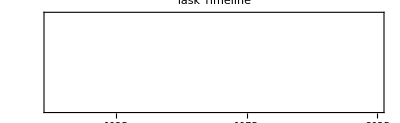

```mathematica
(*Create a timeline plot*)
timelinePlots=TimelinePlot[dateIntervals/. {task_,interval_}:>Style[task,Blue],PlotLabel->"Task Timeline",ImageSize->Large];

timelinePlots
```

```mathematica
DateObject[{"Wednesday","5:00 PM"},{"DayName","Hour12:Minute AMPM"}]
```

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

DateObject[{Wednesday,5:00 PM},{DayName,Hour12:Minute AMPM}]

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

DateInterval::arg: Argument {DateObject[{Wednesday,5:00 PM},{DayName,Hour12:Minute AMPM}],DateObject[{Thursday,12:00 AM},{DayName,Hour12:Minute AMPM}]} cannot be interpreted as a date or time input.

DateObject::notgran: {DayName,Hour12:Minute AMPM} is not a valid granularity specification for calendar Automatic.

General::stop: Further output of DateObject::notgran will be suppressed during this calculation.

DateInterval::arg: Argument {DateObject[{Thursday,9:00 AM},{DayName,Hour12:Minute AMPM}],DateObject[{Thursday,5:00 PM},{DayName,Hour12:Minute AMPM}]} cannot be interpreted as a date or time input.

DateInterval::arg: Argument {DateObject[{Friday,9:00 AM},{DayName,Hour12:Minute AMPM}],DateObject[{Friday,5:00 PM},{DayName,Hour12:Minute AMPM}]} cannot be interpreted as a date or time input.

General::stop: Further output of DateInterval::arg will be suppressed during this calculation.

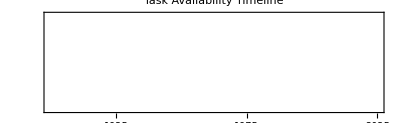

```mathematica
schedule={<|"Day"->"Wednesday","Time"->"5:00 PM - 12:00 AM","Task"->"Available"|>,<|"Day"->"Thursday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,<|"Day"->"Friday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,<|"Day"->"Saturday","Time"->"9:00 AM - 5:00 PM","Task"->"Available"|>,<|"Day"->"Sunday","Time"->"7:00 PM - 12:00 AM","Task"->"Available"|>};

(*Manually create DateIntervals*)
dateIntervals={{"Available",DateInterval[{DateObject[{"Wednesday","5:00 PM"},{"DayName","Hour12:Minute AMPM"}],DateObject[{"Thursday","12:00 AM"},{"DayName","Hour12:Minute AMPM"}]}]},{"Available",DateInterval[{DateObject[{"Thursday","9:00 AM"},{"DayName","Hour12:Minute AMPM"}],DateObject[{"Thursday","5:00 PM"},{"DayName","Hour12:Minute AMPM"}]}]},{"Available",DateInterval[{DateObject[{"Friday","9:00 AM"},{"DayName","Hour12:Minute AMPM"}],DateObject[{"Friday","5:00 PM"},{"DayName","Hour12:Minute AMPM"}]}]},{"Available",DateInterval[{DateObject[{"Saturday","9:00 AM"},{"DayName","Hour12:Minute AMPM"}],DateObject[{"Saturday","5:00 PM"},{"DayName","Hour12:Minute AMPM"}]}]},{"Available",DateInterval[{DateObject[{"Sunday","7:00 PM"},{"DayName","Hour12:Minute AMPM"}],DateObject[{"Monday","12:00 AM"},{"DayName","Hour12:Minute AMPM"}]}]}};

(*Plot the timeline*)
TimelinePlot[dateIntervals/. {task_,interval_}:>Style[task,Blue],PlotLabel->"Task Availability Timeline",ImageSize->Large]
```

```mathematica
(*Define Schedule Starting from Today (January 15,2025)*)schedule={<|"Day"->"Wednesday","Date"->{2025,1,15},"Time"->"9:00 AM - 10:00 AM","Task"->"Morning Standup"|>,<|"Day"->"Thursday","Date"->{2025,1,16},"Time"->"10:00 AM - 11:30 AM","Task"->"Project Planning"|>,<|"Day"->"Friday","Date"->{2025,1,17},"Time"->"2:00 PM - 3:30 PM","Task"->"Team Review"|>,<|"Day"->"Saturday","Date"->{2025,1,18},"Time"->"11:00 AM - 1:00 PM","Task"->"Weekend Workshop"|>,<|"Day"->"Sunday","Date"->{2025,1,19},"Time"->"3:00 PM - 4:30 PM","Task"->"Weekly Recap"|>};

(*Convert Schedule to Timeline Data*)
timelineData=Table[Placed[schedule[[i,"Task"]],Above]->Interval[{DateObject[Join[schedule[[i,"Date"]],ToExpression[StringReplace[schedule[[i,"Time"]],RegularExpression["(.*?):.*"]->"$1"]]],DateObject[Join[schedule[[i,"Date"]],ToExpression[StringReplace[schedule[[i,"Time"]],RegularExpression[".*?-(.*?):.*"]->"$1"]]]}
],{i,Length[schedule]}
];

(*Generate the Timeline Plot*)
TimelinePlot[timelineData,PlotLabel->"Schedule for This Week",LabelStyle->{Bold,14},PlotTheme->"Detailed"]
```

```mathematica
DateObject["Wednesday 5:00pm"]
```

Wed 1 Jan 2025 17:00:00GMT-7

```mathematica
DateValue[DateObject[{2025,1,1,17,0,0},"Instant","Gregorian",-7.],"Hour"]
```

17

```mathematica
"month calendar"DateObject[{2025,1,1,17,0,0},"Instant","Gregorian",-7.]With[{year=DateValue[DateObject[{2025,1,1,17,0,0},"Instant","Gregorian",-7.],"Year"],month=DateValue[DateObject[{2025,1,1,17,0,0},"Instant","Gregorian",-7.],"Month"],daynames={Sunday,Monday,Tuesday,Wednesday,Thursday,Friday,Saturday},abbrevs={"Su","Mo","Tu","We","Th","Fr","Sa"}},Labeled[TableForm[Partition[Range[QuantityMagnitude[DateDifference[{year,month},If[month==12,{year+1,1},{year,month+1}]]]],7,7,{DayName[{year,month,1}]/.Thread[daynames->Range[7]],1},""],TableHeadings->{None,abbrevs},TableSpacing->{1,1}],DateString[DateObject[{year,month}]],Top]]
```

```mathematica
{{"Su", "Mo", "Tu", "We", "Th", "Fr", "Sa"}, {"", "", "", 1, 2, 3, 4}, {5, 6, 7, 8, 9, □, 11}, {12, 13, 14, 15, 16, 17, 18}, {19, 20, 21, 22, 23, 24, 25}, {26, 27, 28, 29, 30, 31, ""}}"Jan 2025"
```

```mathematica
TimelinePlot[DateInterval[{DateObject["Wednesday 5:00pm"], DateObject["Wednesday 11:59pm"]}]]
```

-Graphics-

```mathematica
Labeled[TimelinePlot[%289], Tomorrow, Left]
```

-Graphics-Thu 16 Jan 2025

```mathematica
DateInterval[{DateObject[{2025, 1, 14, 9}], DateObject[{2025, 1, 19}]}, "Day"]
```

DateInterval[…]

```mathematica
TimelinePlot[%287]
```

-Graphics-

```mathematica
DateInterval[{DateObject["Jan 15 5:00 PM"],DateObject["Jan 15 11:59 PM"]}][[1]]
```

TimeZoneOffset::date: Expression {Automatic,1,15,5,0,Automatic} cannot be interpreted as a date specification.

TimeZoneOffset::date: Expression {Automatic,1,15,11,59,Automatic} cannot be interpreted as a date specification.

{{{2025,1,15,5,0,0.},{2025,1,15,11,59,0.}}}

```mathematica
TimeObject[{9, 0, 0}]
```

09:00:00TimeObject[{9,0,0},Instant]

```mathematica
DateObject["Jan 16 5:00 PM"]
```

TimeZoneOffset::date: Expression {Automatic,1,16,5,0,Automatic} cannot be interpreted as a date specification.

Thu 16 Jan 2025 05:00:00GMT-7

```mathematica
{DateInterval[{DateObject["Jan 15 5:00 PM"],DateObject["Jan 15 11:59 PM"]}],DateInterval[{DateObject["Jan 16 9:00 AM"],DateObject["Jan 16 17:00"]}],DateInterval[{DateObject["Jan 17 9:00 AM"],DateObject["Jan 17 17:00"]}],DateInterval[{DateObject["Jan 18 9:00 AM"],DateObject["Jan 18 17:00"]}],DateInterval[{DateObject["Jan 19 7:00 PM"],DateObject["Jan 19 23:59"]}]}
```

TimeZoneOffset::date: Expression {Automatic,1,15,5,0,Automatic} cannot be interpreted as a date specification.

TimeZoneOffset::date: Expression {Automatic,1,15,11,59,Automatic} cannot be interpreted as a date specification.

TimeZoneOffset::date: Expression {Automatic,1,16,9,0,Automatic} cannot be interpreted as a date specification.

General::stop: Further output of TimeZoneOffset::date will be suppressed during this calculation.

{DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…],DateInterval[…]}

```mathematica
TimelinePlot[#, PlotRange-> {DateObject[Append[#[[1, 1, 1, ;;3]], 9]],DateObject[Append[#[[1, 1, 2, ;;3]], 24]]}]& /@{DateInterval[{DateObject["Jan 15 5:00 PM"],DateObject["Jan 15 11:59 PM"]}],DateInterval[{DateObject["Jan 16 9:00 AM"],DateObject["Jan 16 17:00"]}],DateInterval[{DateObject["Jan 17 9:00 AM"],DateObject["Jan 17 17:00"]}],DateInterval[{DateObject["Jan 18 9:00 AM"],DateObject["Jan 18 17:00"]}],DateInterval[{DateObject["Jan 19 7:00 PM"],DateObject["Jan 19 23:59"]}]}
```

TimeZoneOffset::date: Expression {Automatic,1,15,5,0,Automatic} cannot be interpreted as a date specification.

TimeZoneOffset::date: Expression {Automatic,1,15,11,59,Automatic} cannot be interpreted as a date specification.

TimeZoneOffset::date: Expression {Automatic,1,16,9,0,Automatic} cannot be interpreted as a date specification.

General::stop: Further output of TimeZoneOffset::date will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TimelinePlot[{DateInterval[{DateObject["Wednesday 5:00 PM"],DateObject["Wednesday 11:59 PM"]}],DateInterval[{DateObject["Thursday 9:00 AM"],DateObject["Thursday 5:00 PM"]}],DateInterval[{DateObject["Friday 9:00 AM"],DateObject["Friday 5:00 PM"]}],DateInterval[{DateObject["Saturday 9:00 AM"],DateObject["Saturday 5:00 PM"]}],DateInterval[{DateObject["Sunday 7:00 PM"],DateObject["Sunday 11:59 PM"]}]},PlotLabel->"Task Availability Timeline",ImageSize->Large]
```

TimeZoneOffset::date: Expression {Automatic,Automatic,Automatic,5,0,Automatic} cannot be interpreted as a date specification.

TimeZoneOffset::date: Expression {Automatic,Automatic,Automatic,11,59,Automatic} cannot be interpreted as a date specification.

TimeZoneOffset::date: Expression {Automatic,Automatic,Automatic,9,0,Automatic} cannot be interpreted as a date specification.

General::stop: Further output of TimeZoneOffset::date will be suppressed during this calculation.

-Graphics-